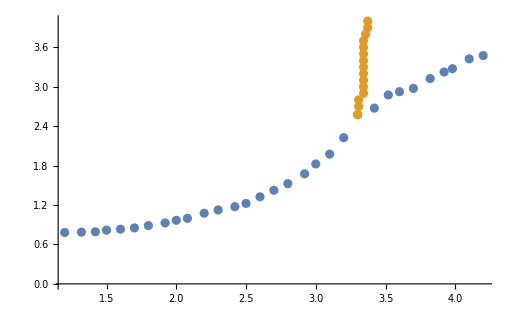

```mathematica
ee={{1,(0.355+0.36)/2},{1.1,(0.375+0.37)/2},{1.2,(0.385+0.38)/2},{1.3,(0.395+0.39)/2},{1.4,(0.405+0.41)/2},{1.5,(0.425+0.43)/2},{1.6,(0.445+0.44)/2},{1.7,(0.455+0.46)/2},{1.8,(0.475+0.47)/2},{1.9,(0.495+0.49)/2},{2.0,(0.515+0.52)/2},{2.1,(0.545+0.54)/2},{2.2,(0.565+0.56)/2},{2.3,(0.585+0.59)/2},{2.4,(0.615+0.61)/2},{2.5,(0.655+0.65)/2},{2.6,(0.685+0.68)/2},{2.7,(0.705+0.70)/2},{2.8,(0.715+0.71)/2},{2.9,(0.725+0.72)/2},{3.0,(0.735+0.73)/2},{3.1,(0.735+0.74)/2},{3.2,(0.745+0.75)/2},{3.3,(0.755+0.75)/2},{3.4,(0.755+0.76)/2},{3.5,(0.765+0.77)/2},{3.6,(0.775+0.77)/2},{3.7,(0.775+0.78)/2},{3.8,(0.785+0.78)/2},{3.9,(0.785+0.79)/2},{4.0,(0.795+0.79)/2}};
ff={{(2.655+2.66)/2,0.7},{(2.715+2.72)/2,0.8},{(2.75+2.745)/2,0.9},{(2.81+2.815)/2,1.0},{(2.84+2.845)/2,1.1},{(2.87+2.875)/2,1.2},{(2.91+2.905)/2,1.3},{(2.94+2.935)/2,1.4},{(2.965+2.97)/2,1.5},{(2.965+2.97)/2,1.6},{(2.995+3.0)/2,1.7},{(2.995+3.0)/2,1.8},{(3.035+3.03)/2,1.9},{(3.035+3.03)/2,2.0},{(3.065+3.06)/2,2.1},{(3.065+3.06)/2,2.2},{(3.065+3.06)/2,2.3},{(3.095+3.09)/2,2.4},{(3.095+3.09)/2,2.5},{(3.095+3.09)/2,2.6},{(3.095+3.09)/2,2.7},{(3.125+3.12)/2,2.8},{(3.125+3.12)/2,2.9},{(3.125+3.12)/2,3.0},{(3.125+3.12)/2,3.1},{(3.125+3.12)/2,3.2},{(3.125+3.12)/2,3.3},{(3.155+3.16)/2,3.4},{(3.155+3.16)/2,3.5},{(3.155+3.16)/2,3.6},{(3.155+3.16)/2,3.7},{(3.155+3.16)/2,3.8},{(3.155+3.16)/2,3.9},{(3.155+3.16)/2,4.0}};
ee2={{1-0.2,(0.135+0.14)/2},{1.1-0.2,(0.145+0.15)/2},{1.2-0.2,(0.16+0.155)/2},{1.3-0.2,(0.16+0.165)/2},{1.4-0.2,(0.165+0.17)/2},{1.5-0.2,(0.175+0.18)/2},{1.6-0.2,(0.185+0.18)/2},{1.7-0.2,(0.195+0.19)/2},{1.8-0.2,(0.195+0.2)/2},{1.9-0.2,(0.215+0.21)/2},{2-0.2,(0.215+0.22)/2},{2.1-0.2,(0.225+0.23)/2},{2.2-0.2,(0.225+0.23)/2},{2.3-0.2,(0.225+0.23)/2},{2.4-0.2,(0.235+0.23)/2},{2.5-0.2,(0.225+0.23)/2},{2.6-0.2,(0.235+0.23)/2},{2.7-0.2,(0.235+0.23)/2},{2.8-0.2,(0.235+0.23)/2},{2.9-0.2,(0.235+0.23)/2},{3-0.2,(0.225+0.25)/2},{3-0.2,(0.225+0.25)/2},{3.1-0.2,(0.225+0.25)/2},{3.2-0.2,(0.235+0.24)/2},{3.3-0.2,(0.235+0.24)/2},{3.4-0.2,(0.235+0.24)/2},{3.5-0.2,(0.235+0.23)/2},{3.6-0.2,(0.235+0.23)/2},{3.7-0.2,(0.235+0.24)/2},{3.8-0.2,(0.235+0.24)/2},{3.9-0.2,(0.235+0.24)/2},{4.0-0.2,(0.235+0.23)/2}};
ff2={{2.1-0.2,(0.225+0.23)/2},{(2.17+2.165)/2-0.2, 0.3},{(2.3+2.295)/2-0.2, 0.4},{(2.41+2.405)/2-0.2, 0.5},{(2.5+2.505)/2-0.2, 0.6},{(2.57+2.575)/2-0.2,0.7},{(2.64+2.645)/2-0.2,0.8},{(2.7+2.695)/2-0.2,0.9},{(2.745+2.75)/2-0.2,1},{(2.785+2.78)/2-0.2,1.1},{(2.825+2.82)/2-0.2,1.2},{(2.855+2.85)/2-0.2,1.3},{(2.885+2.88)/2-0.2,1.4},{(2.905+2.91)/2-0.2,1.5},{(2.935+2.93)/2-0.2,1.6},{(2.955+2.95)/2-0.2,1.7},{(2.975+2.97)/2-0.2,1.8},{(2.995+2.99)/2-0.2,1.9},{(3.005+3.0)/2-0.2,2.0},{(3.025+3.02)/2-0.2,2.1},{(3.035+3.03)/2-0.2,2.2},{(3.045+3.04)/2-0.2,2.3},{(3.055+3.06)/2-0.2,2.4},{(3.065+3.07)/2-0.2,2.5},{(3.075+3.07)/2-0.2,2.6},{(3.085+3.08)/2-0.2,2.7},{(3.095+3.09)/2-0.2,2.8},{(3.095+3.1)/2-0.2,2.9},{(3.105+3.1)/2-0.2,3.0},{(3.105+3.11)/2-0.2,3.1},{(3.115+3.12)/2-0.2,3.2},{(3.125+3.12)/2-0.2,3.3},{(3.125+3.12)/2-0.2,3.4},{(3.125+3.13)/2-0.2,3.5},{(3.125+3.13)/2-0.2,3.6},{(3.135+3.13)/2-0.2,3.7},{(3.145+3.14)/2-0.2,3.8},{(3.145+3.15)/2-0.2,3.9},{(3.155+3.15)/2-0.2,4.0}};
ee3={{1+0.2,(0.78+0.785)/2},{1.12+0.2,(0.79+0.785)/2},{1.22+0.2,(0.79+0.795)/2},{1.3+0.2,(0.815+0.82)/2},{1.4+0.2,(0.835+0.83)/2},{1.5+0.2,(0.855+0.85)/2},{1.6+0.2,(0.885+0.89)/2},{1.72+0.2,(0.925+0.93)/2},{1.8+0.2,(0.965+0.97)/2},{1.88+0.2,(0.995+1.0)/2},{2+0.2,(1.05+1.1)/2},{2.1+0.2,(1.15+1.1)/2},{2.22+0.2,(1.15+1.2)/2},{2.3+0.2,(1.2+1.25)/2},{2.4+0.2,(1.3+1.35)/2},{2.5+0.2,(1.4+1.45)/2},{2.6+0.2,(1.5+1.55)/2},{2.72+0.2,(1.7+1.65)/2},{2.8+0.2,(1.8+1.85)/2},{2.9+0.2,(2.0+1.95)/2},{3+0.2,(2.2+2.25)/2},{3.1+0.2,(2.6+2.55)/2},{3.22+0.2,(2.7+2.65)/2},{3.32+0.2,(2.9+2.85)/2},{3.4+0.2,(2.9+2.95)/2},{3.5+0.2,(3.0+2.95)/2},{3.62+0.2,(3.1+3.15)/2},{3.72+0.2,(3.2+3.25)/2},{3.78+0.2,(3.3+3.25)/2},{3.9+0.2,(3.4+3.45)/2},{4.0+0.2,(3.5+3.45)/2}};
ff3={{3.1+0.2,(2.6+2.55)/2},{(3.11+3.105)/2+0.2,2.7},{(3.11+3.105)/2+0.2,2.8},{(3.14+3.145)/2+0.2,2.9},{(3.14+3.145)/2+0.2,3},{(3.14+3.145)/2+0.2,3.1},{(3.14+3.145)/2+0.2,3.2},{(3.14+3.145)/2+0.2,3.3},{(3.14+3.145)/2+0.2,3.4},{(3.14+3.145)/2+0.2,3.5},{(3.14+3.145)/2+0.2,3.6},{(3.14+3.145)/2+0.2,3.7},{(3.16+3.155)/2+0.2,3.8},{(3.17+3.175)/2+0.2,3.9},{(3.17+3.175)/2+0.2,4.0}};
ListPlot[{ee3,ff3}]
```

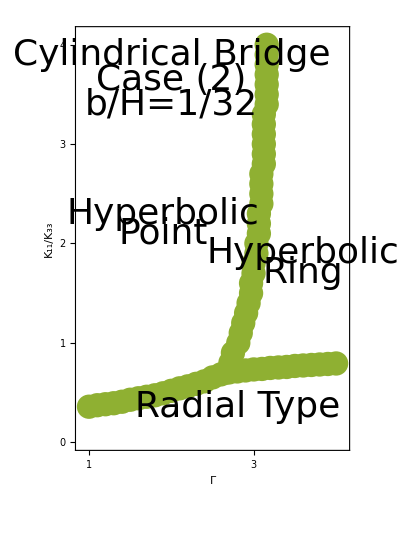

```mathematica
ListPlot[{ee,ff},PlotStyle->{{Thickness[0.005],RGBColor[0.560181,0.691569,0.194885]}, {Thickness[0.005],RGBColor[0.560181,0.691569,0.194885]}},Joined->{True, True},PlotMarkers->{Graphics[{Disk[]},ImageSize->25],Graphics[{Disk[]},ImageSize->25]}, PlotRange->{{0.9,4.1},{0,4.1}}, Frame->{True, True, True, True}, FrameTicks->{{{0,1,2,3,4},None},{{1,2,3,4,5,6},None}},FrameTicksStyle->Directive[Black,36],LabelStyle->Directive[Black,36],FrameLabel->{{"K_11/K_33", None},{"Γ", None}},FrameStyle->Thickness[0.005],Epilog->{Text[Style["Cylindrical Bridge",Directive[Black,36]],{2,3.9}],
Text[Style["Case (2)",Directive[Black,36]],{2,3.65}],
Text[Style["b/H=1/32",Directive[Black,36]],{2,3.4}],
Text[Style["Hyperbolic",Directive[Black,36]],{1.9,2.3}],Text[Style["Point",Directive[Black,36]],{1.9,2.1}],Text[Style["Hyperbolic",Directive[Black,36]],{3.6,1.9}],
Text[Style["Ring",Directive[Black,36]],{3.6,1.7}],
Text[Style["Radial Type",Directive[Black,36]],{2.8,0.35}]},AspectRatio->4/3]
```

```mathematica
ColorData[97,"ColorList"]//InputForm
```

{RGBColor[0.368417, 0.506779, 0.709798], RGBColor[0.880722, 0.611041, 0.142051], 
 RGBColor[0.560181, 0.691569, 0.194885], RGBColor[0.922526, 0.385626, 0.209179], 
 RGBColor[0.528488, 0.470624, 0.701351], RGBColor[0.772079, 0.431554, 0.102387], 
 RGBColor[0.363898, 0.618501, 0.782349], RGBColor[1, 0.75, 0], 
 RGBColor[0.647624, 0.37816, 0.614037], RGBColor[0.571589, 0.586483, 0.], 
 RGBColor[0.915, 0.3325, 0.2125], RGBColor[0.40082222609352647, 0.5220066643438841, 
  0.85], RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142], 
 RGBColor[0.736782672705901, 0.358, 0.5030266573755369], 
 RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

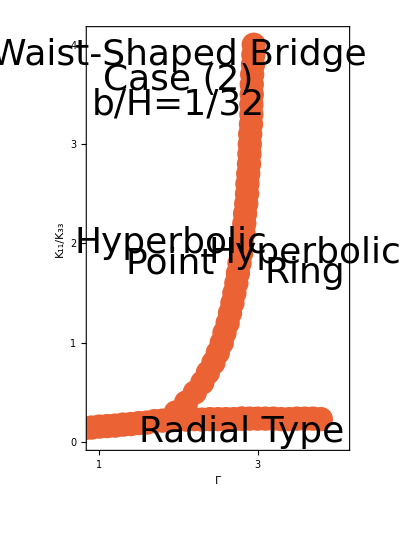

```mathematica
ListPlot[{ee2,ff2},PlotStyle->{{Thickness[0.005],RGBColor[0.922526,0.385626,0.209179]}, {Thickness[0.005],RGBColor[0.922526,0.385626,0.209179]}},Joined->{True, True},PlotMarkers->{Graphics[{Disk[]},ImageSize->25],Graphics[{Disk[]},ImageSize->25]}, PlotRange->{{0.9,4.1},{0,4.1}}, Frame->{True, True, True, True}, FrameTicks->{{{0,1,2,3,4},None},{{1,2,3,4,5,6},None}},FrameTicksStyle->Directive[Black,36],LabelStyle->Directive[Black,36],FrameLabel->{{"K_11/K_33", None},{"Γ", None}},FrameStyle->Thickness[0.005],Epilog->{Text[Style["Waist-Shaped Bridge",Directive[Black,36]],{2,3.9}],
Text[Style["Case (2)",Directive[Black,36]],{2,3.65}],
Text[Style["b/H=1/32",Directive[Black,36]],{2,3.4}],
Text[Style["Hyperbolic",Directive[Black,36]],{1.9,2.0}],Text[Style["Point",Directive[Black,36]],{1.9,1.8}],Text[Style["Hyperbolic",Directive[Black,36]],{3.6,1.9}],
Text[Style["Ring",Directive[Black,36]],{3.6,1.7}],
Text[Style["Radial Type",Directive[Black,36]],{2.8,0.1}]},AspectRatio->4/3]
```

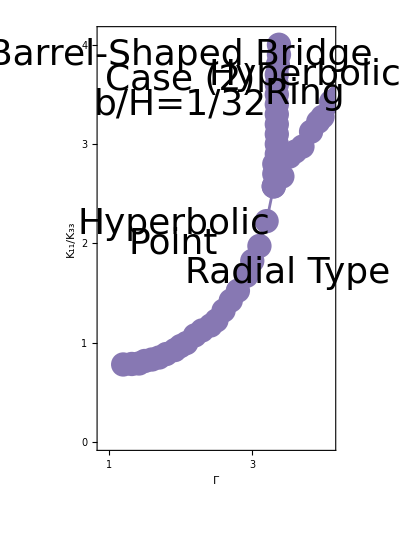

```mathematica
ListPlot[{ee3,ff3},PlotStyle->{{Thickness[0.005],RGBColor[0.528488,0.470624,0.701351]}, {Thickness[0.005],RGBColor[0.528488,0.470624,0.701351]}},Joined->{True, True},PlotMarkers->{Graphics[{Disk[]},ImageSize->25],Graphics[{Disk[]},ImageSize->25]}, PlotRange->{{0.9,4.1},{0,4.1}}, Frame->{True, True, True, True}, FrameTicks->{{{0,1,2,3,4},None},{{1,2,3,4,5,6},None}},FrameTicksStyle->Directive[Black,36],LabelStyle->Directive[Black,36],FrameLabel->{{"K_11/K_33", None},{"Γ", None}},FrameStyle->Thickness[0.005],Epilog->{Text[Style["Barrel-Shaped Bridge",Directive[Black,36]],{2,3.9}],
Text[Style["Case (2)",Directive[Black,36]],{2,3.65}],
Text[Style["b/H=1/32",Directive[Black,36]],{2,3.4}],
Text[Style["Hyperbolic",Directive[Black,36]],{1.9,2.2}],Text[Style["Point",Directive[Black,36]],{1.9,2.0}],Text[Style["Hyperbolic",Directive[Black,36]],{3.736,3.7}],
Text[Style["Ring",Directive[Black,36]],{3.736,3.5}],
Text[Style["Radial Type",Directive[Black,36]],{3.5,1.7}]},AspectRatio->4/3]
```

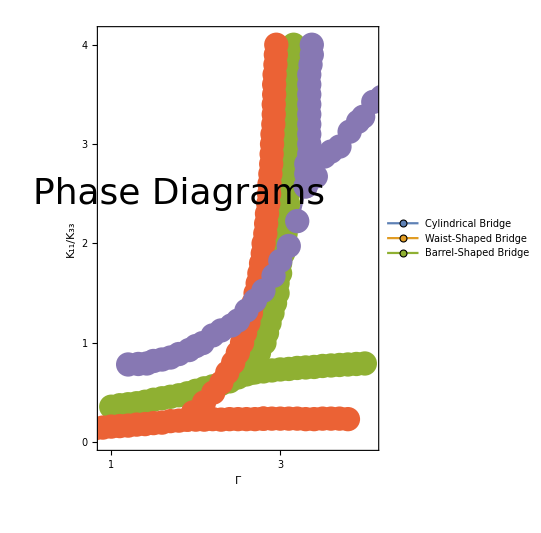

```mathematica
ListPlot[{ee,ff,ee2,ff2,ee3,ff3},PlotStyle->{{Thickness[0.005],RGBColor[0.560181,0.691569,0.194885]}, {Thickness[0.005],RGBColor[0.560181,0.691569,0.194885]},
{Thickness[0.005],RGBColor[0.922526,0.385626,0.209179]}, {Thickness[0.005],RGBColor[0.922526,0.385626,0.209179]},
{Thickness[0.005],RGBColor[0.528488,0.470624,0.701351]}, {Thickness[0.005],RGBColor[0.528488,0.470624,0.701351]}},Joined->{True, True,True, True,True, True}, PlotRange->{{0.9,4.1},{0,4.1}}, Frame->{True, True, True, True}, PlotLegends->Placed[PointLegend[{RGBColor[0.368417,0.506779,0.709798], RGBColor[0.880722,0.611041,0.142051], RGBColor[0.560181,0.691569,0.194885]},{"Cylindrical Bridge","Waist-Shaped Bridge","Barrel-Shaped Bridge"},LegendMarkers->{{Graphics[Disk[]],25},{Graphics[Disk[]],25},{Graphics[Disk[]],25}}],{Left, Top}],PlotMarkers->{Graphics[{Disk[]},ImageSize->25],Graphics[{Disk[]},ImageSize->25]},FrameTicks->{{{0,1,2,3,4},None},{{1,2,3,4,5,6},None}},FrameTicksStyle->Directive[Black,36],LabelStyle->Directive[Black,36],FrameLabel->{{"K_11/K_33", None},{"Γ", None}},FrameStyle->Thickness[0.005],Epilog->{Text[Style["Phase Diagrams",Directive[Black,36]],{1.8,2.5}]},AspectRatio->4/3]
```